```mathematica
(*43 had no exercises*)
```

```mathematica
(*44.1*)
```

```mathematica
Import["https://www.google.com","Images"]
```

{-Graphics-}

```mathematica
(*44.2*)
```

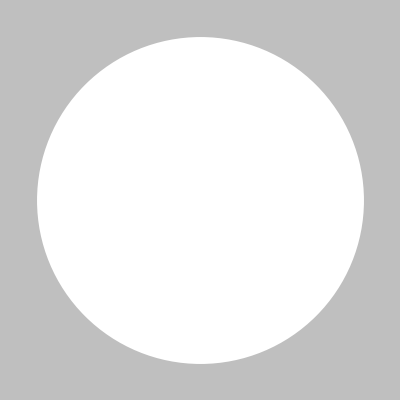
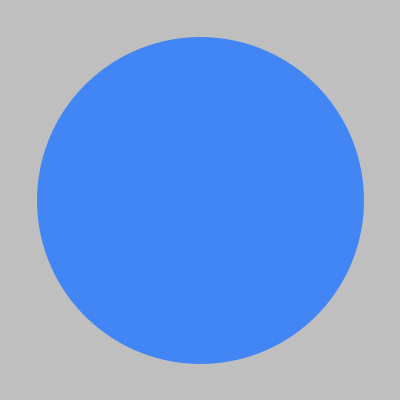
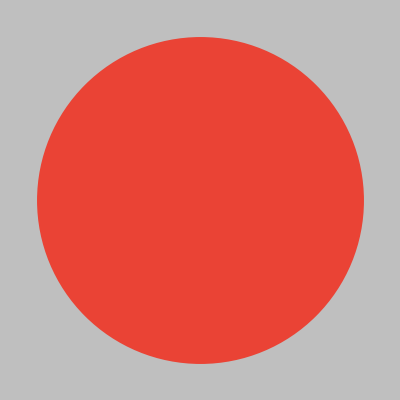
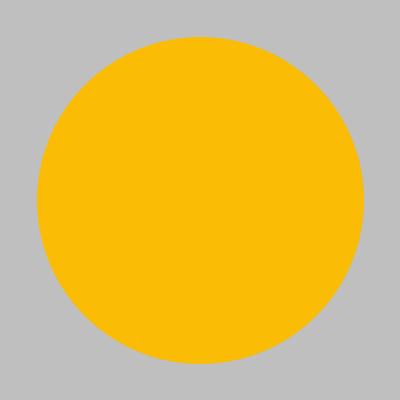
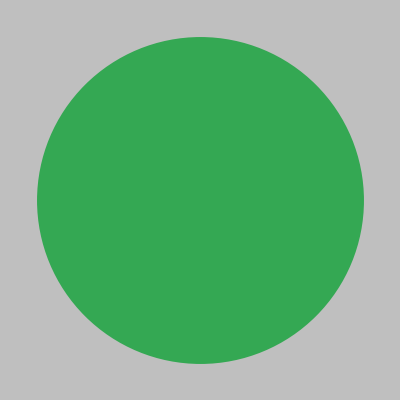

```mathematica
Graphics[Style[Disk[],#],Background->Lighter[Gray, 0.5]]&/@Flatten[DominantColors[Import["https://www.google.com","Images"]]]
```

```mathematica
(*44.3*)
```

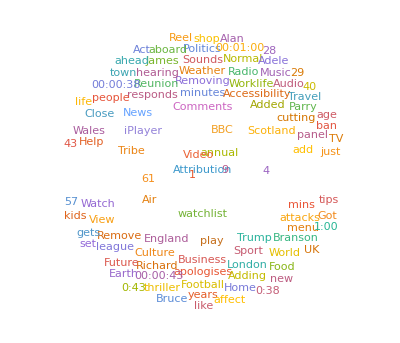

```mathematica
WordCloud[Import["http://bbc.co.uk/"] ]
```

```mathematica
(*44.4*)
```

```mathematica
ImageCollage[Import["https://nps.gov","Images"]]
```

-Graphics-

```mathematica
Select[Import["https://en.wikipedia.org/wiki/Ostrich","Images"],ImageInstanceQ[#,"bird"]&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*44.6 unallowed to access NATO for some reason. I just used the wikipedia page for NATO*)
```

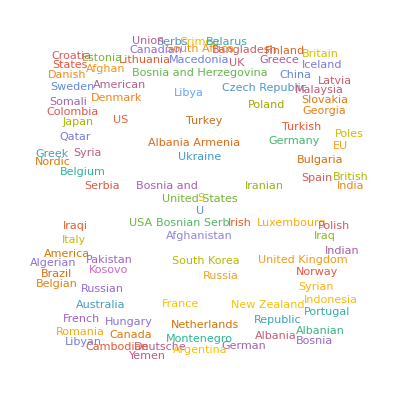

```mathematica
WordCloud[TextCases[Import["https://en.wikipedia.org/wiki/NATO"],"Country"]]
```

```mathematica
(*44.7*)Length[Import[,]]
```

362

```mathematica
(*44.8*)SendMail[GeoGraphics[$GeoLocation]]
```

Success[…]

```mathematica
(*44.9*)SendMail[MoonPhase[]]
```

Success[…]